```mathematica
<|"Vivax"-><|data...|>,"Falciparum"-><|data...|>|>
```

<|Vivax→Association[data...],Falciparum→Association[data...]|>

```mathematica
ClearAll[rulify]
rulify[data_List]:=AssociationThread[{DateObject[{2011},"Year"],DateObject[{2012},"Year"],DateObject[{2013},"Year"],DateObject[{2014},"Year"]}->data]
```

```mathematica
plasmodiumVivaxPatients=rulify[{38,70,75,56}];
plasmodiumFalciparumPatients=rulify[{2,19,10,5}];
```

```mathematica
patientdata=<|"VivaxPatients"->plasmodiumVivaxPatients,"FalciparumPatients"->plasmodiumFalciparumPatients|>
```

<|VivaxPatients→<|Year: 2011→38,Year: 2012→70,Year: 2013→75,Year: 2014→56|>,FalciparumPatients→<|Year: 2011→2,Year: 2012→19,Year: 2013→10,Year: 2014→5|>|>

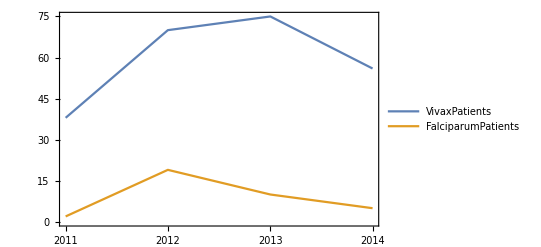

```mathematica
DateListPlot[patientdata]
```

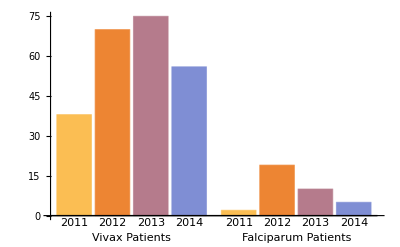

```mathematica
BarChart[patientdata,ChartLabels->{{"Vivax Patients","Falciparum Patients"},{"2011","2012","2013","2014"}}]
```

```mathematica
populationdata=rulify[{42879.69,44185.5,45531.5,46917.8}]
```

<|Year: 2011→42879.7,Year: 2012→44185.5,Year: 2013→45531.5,Year: 2014→46917.8|>

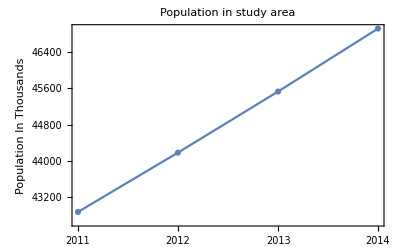

```mathematica
DateListPlot[populationdata,PlotMarkers->Automatic,PlotLabel->"Population in study area",Frame->{{True,False},{True,False}},FrameLabel->{"","Population In Thousands"}]
```

```mathematica
?*Chart
```

```mathematica
ageGroupKeys=Map[StringRiffle[#,"to"]&]@Partition[Range[0,65,5],2,1]
```

{0to5,5to10,10to15,15to20,20to25,25to30,30to35,35to40,40to45,45to50,50to55,55to60,60to65}

```mathematica
femaleMalariaCases=AssociationThread[ageGroupKeys->{3,1,2,4,3,1,2,3,2,2,3,2,3}]
```

<|0to5→3,5to10→1,10to15→2,15to20→4,20to25→3,25to30→1,30to35→2,35to40→3,40to45→2,45to50→2,50to55→3,55to60→2,60to65→3|>

```mathematica
maleMalariaCases=AssociationThread[ageGroupKeys->{2,2,1,1,3,2,4,4,1,1,1,1,1}]
```

<|0to5→2,5to10→2,10to15→1,15to20→1,20to25→3,25to30→2,30to35→4,35to40→4,40to45→1,45to50→1,50to55→1,55to60→1,60to65→1|>

```mathematica
confirmedMalariaCases=<|"Male"->femaleMalariaCases,"Female"->maleMalariaCases|>
```

<|Male→<|0to5→3,5to10→1,10to15→2,15to20→4,20to25→3,25to30→1,30to35→2,35to40→3,40to45→2,45to50→2,50to55→3,55to60→2,60to65→3|>,Female→<|0to5→2,5to10→2,10to15→1,15to20→1,20to25→3,25to30→2,30to35→4,35to40→4,40to45→1,45to50→1,50to55→1,55to60→1,60to65→1|>|>

```mathematica
PairedBarChart[(*Data to compare*)confirmedMalariaCases["Male"],confirmedMalariaCases["Female"],(*Styling Options*)ChartStyle->"Pastel",ChartLabels->{{"Male","Female"},None,ageGroupKeys},PlotLabel->"Malaria Cases for Various Age Groups"]
```

-Graphics-

```mathematica
malariaPatientOccupations=<|"Labor"-><|"NumberOfHouses"->40,"NumberOfPatients"->100|>,"Agricultural"-><|"NumberOfHouses"->18,"NumberOfPatients"->70|>,"Business"-><|"NumberOfHouses"->14,"NumberOfPatients"->30|>,"Jobholders"-><|"NumberOfHouses"->11,"NumberOfPatients"->20|>,"Other"-><|"NumberOfHouses"->7,"NumberOfPatients"->30|>|>
```

<|Labor→<|NumberOfHouses→40,NumberOfPatients→100|>,Agricultural→<|NumberOfHouses→18,NumberOfPatients→70|>,Business→<|NumberOfHouses→14,NumberOfPatients→30|>,Jobholders→<|NumberOfHouses→11,NumberOfPatients→20|>,Other→<|NumberOfHouses→7,NumberOfPatients→30|>|>

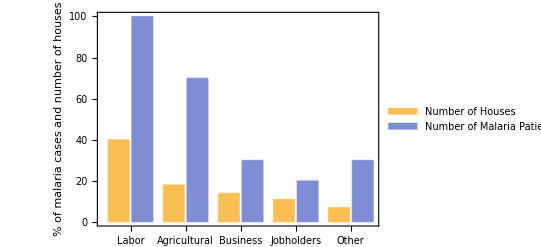

```mathematica
BarChart[malariaPatientOccupations,(*Options*)ChartLabels->{{"Labor","Agricultural","Business","Jobholders","Other"},None},ChartLegends->{"Number of Houses","Number of Malaria Patients"},Frame->{{True,False},{True,False}},FrameLabel->{"","% of malaria cases and number of houses"}]
```

```mathematica
freq=MapThread[{#1,#2,Splice[#3]}&,{(*Year*){"2011","2012","2013","2014"},{543,682,376,600},{{26,26,21,24,24,34,45,84,103,92,36,28},{8,65,89,74,89,68,32,43,67,74,53,20},{9,12,37,27,48,23,45,27,37,35,58,18},{30,36,51,93,111,30,30,35,60,36,59,29}}}]
```

{{2011,543,26,26,21,24,24,34,45,84,103,92,36,28},{2012,682,8,65,89,74,89,68,32,43,67,74,53,20},{2013,376,9,12,37,27,48,23,45,27,37,35,58,18},{2014,600,30,36,51,93,111,30,30,35,60,36,59,29}}

```mathematica
TableForm[freq,TableHeadings->{None,{"Year","Total","Jan","Feb","Mar","Apr","May","Jun","Jul","Aug","Sep","Oct","Nov","Dec"}}]
```

Year | Total | Jan | Feb | Mar | Apr | May | Jun | Jul | Aug | Sep | Oct | Nov | Dec
2011 | 543 | 26 | 26 | 21 | 24 | 24 | 34 | 45 | 84 | 103 | 92 | 36 | 28
2012 | 682 | 8 | 65 | 89 | 74 | 89 | 68 | 32 | 43 | 67 | 74 | 53 | 20
2013 | 376 | 9 | 12 | 37 | 27 | 48 | 23 | 45 | 27 | 37 | 35 | 58 | 18
2014 | 600 | 30 | 36 | 51 | 93 | 111 | 30 | 30 | 35 | 60 | 36 | 59 | 29

```mathematica
Column[{Row[{Style["Table 5.1:",Bold]," Frequency of Suspected Malaria Cases in Mubarakpur"}],Grid[{{"Year","Total","Jan","Feb","Mar","Apr","May","Jun","Jul","Aug","Sep","Oct","Nov","Dec"}}~Join~freq,Background->{None,{{None,LightOrange}}},Dividers->{False,{True,True,{False},True}},Spacings->{1,1}]}]
```

Table 5.1: Frequency of Suspected Malaria Cases in Mubarakpur
Year | Total | Jan | Feb | Mar | Apr | May | Jun | Jul | Aug | Sep | Oct | Nov | Dec
2011 | 543 | 26 | 26 | 21 | 24 | 24 | 34 | 45 | 84 | 103 | 92 | 36 | 28
2012 | 682 | 8 | 65 | 89 | 74 | 89 | 68 | 32 | 43 | 67 | 74 | 53 | 20
2013 | 376 | 9 | 12 | 37 | 27 | 48 | 23 | 45 | 27 | 37 | 35 | 58 | 18
2014 | 600 | 30 | 36 | 51 | 93 | 111 | 30 | 30 | 35 | 60 | 36 | 59 | 29

```mathematica
patientfreq=(freq//Map[ReplacePart[2->Nothing]/*(Apply[#1->{##2}&])])//Apply[Association]
```

<|2011→{26,26,21,24,24,34,45,84,103,92,36,28},2012→{8,65,89,74,89,68,32,43,67,74,53,20},2013→{9,12,37,27,48,23,45,27,37,35,58,18},2014→{30,36,51,93,111,30,30,35,60,36,59,29}|>

```mathematica
patientfreq
```

<|2011→{26,26,21,24,24,34,45,84,103,92,36,28},2012→{8,65,89,74,89,68,32,43,67,74,53,20},2013→{9,12,37,27,48,23,45,27,37,35,58,18},2014→{30,36,51,93,111,30,30,35,60,36,59,29}|>

```mathematica
patientsPerMonth=KeyValueMap[Thread[{Map[DateObject/*(#["MonthName"]&)]@Thread[{ToExpression[#1],Range[12]}],#2}]&,patientfreq]
```

{{{January,26},{February,26},{March,21},{April,24},{May,24},{June,34},{July,45},{August,84},{September,103},{October,92},{November,36},{December,28}},{{January,8},{February,65},{March,89},{April,74},{May,89},{June,68},{July,32},{August,43},{September,67},{October,74},{November,53},{December,20}},{{January,9},{February,12},{March,37},{April,27},{May,48},{June,23},{July,45},{August,27},{September,37},{October,35},{November,58},{December,18}},{{January,30},{February,36},{March,51},{April,93},{May,111},{June,30},{July,30},{August,35},{September,60},{October,36},{November,59},{December,29}}}

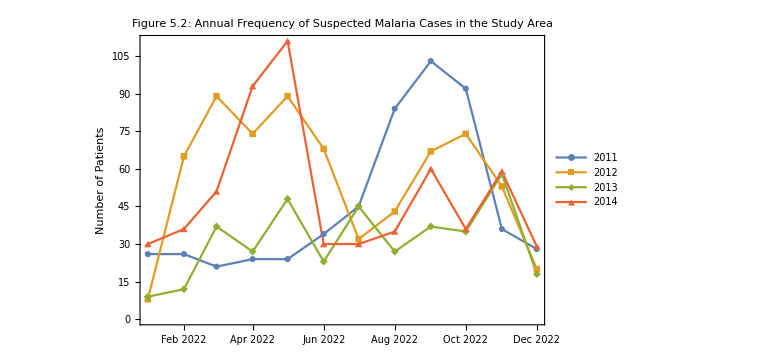

```mathematica
DateListPlot[patientsPerMonth,PlotLegends->{"2011","2012","2013","2014"},PlotMarkers->Automatic,PlotLabel->Row[{Style["Figure 5.2:",Bold]," Annual Frequency of Suspected Malaria Cases in the Study Area"}],Frame->{{True,False},{True,False}},FrameLabel->{"","Number of Patients"},ImageSize->Large]
```

```mathematica
SuspectedMalariaCase=TimeSeries[{{{"January",50},{"February",29},{"March",30},{"April",36},{"May",51},{"June",93},{"July",111},{"August",100},{"September",90},{"October",78},{"November",89},{"December",78}}}];
RainFall=TimeSeries[{{{"January",0},{"February",0},{"March",0},{"April",1},{"May",3},{"June",1},{"July",1},{"August",1},{"September",1},{"October",1},{"November",2},{"December",0}}}];
```

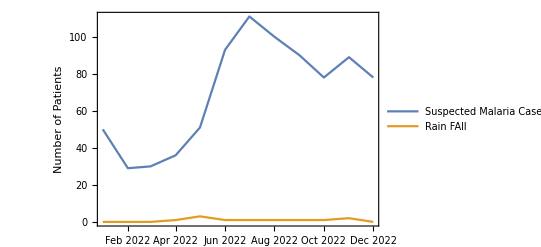

```mathematica
DateListPlot[{SuspectedMalariaCase,RainFall},PlotLegends->{"Suspected Malaria Cases","Rain FAll"},Frame->{{True,False},{True,False}},FrameLabel->{"","Number of Patients"}]
```

Edits begin here.

```mathematica
DateListPlot[patientsPerMonth,
PlotLegends->{"2011","2012","2013","2014"},
PlotMarkers->{{◆,10},{■,10},{▲,10},{\[MathematicaIcon],10}},
PlotLabel->Row[{Style["Figure 5.2:",Bold]," Annual Frequency of Suspected Malaria Cases in the Study Area"}],
Frame->{{True,False},{True,False}},
FrameLabel->{"","Number of Patients"},
Joined->True,
ImageSize->Large]
```

-Graphics-

```mathematica
patientsPerMonth
```

{{{January,26},{February,26},{March,21},{April,24},{May,24},{June,34},{July,45},{August,84},{September,103},{October,92},{November,36},{December,28}},{{January,8},{February,65},{March,89},{April,74},{May,89},{June,68},{July,32},{August,43},{September,67},{October,74},{November,53},{December,20}},{{January,9},{February,12},{March,37},{April,27},{May,48},{June,23},{July,45},{August,27},{September,37},{October,35},{November,58},{December,18}},{{January,30},{February,36},{March,51},{April,93},{May,111},{June,30},{July,30},{August,35},{September,60},{October,36},{November,59},{December,29}}}

```mathematica
populationdata
```

<|Year: 2011→42879.7,Year: 2012→44185.5,Year: 2013→45531.5,Year: 2014→46917.8|>

```mathematica
test=Partition[Range[9],3]
```

{{1,2,3},{4,5,6},{7,8,9}}

```mathematica
test[[All,1]]
```

{1,4,7}

```mathematica
test[[All,2]]
```

{2,5,8}

```mathematica
test[[All,3]]
```

{3,6,9}

```mathematica
patientsPerMonth[[1]]
```

{{January,26},{February,26},{March,21},{April,24},{May,24},{June,34},{July,45},{August,84},{September,103},{October,92},{November,36},{December,28}}

```mathematica
patientsPerMonth[[All,1]]
```

{{January,26},{January,8},{January,9},{January,30}}

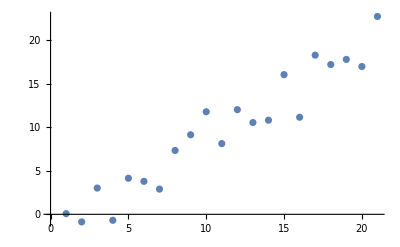

```mathematica
datapts=Table[x+RandomReal[{-4,4}],{x,0,20}];
ListPlot[datapts]
```

```mathematica
datapts
```

{0.0790799,-0.870232,3.01273,-0.686318,4.13796,3.78589,2.89153,7.32639,9.12791,11.7675,8.11301,12.0084,10.5293,10.8021,16.0273,11.1375,18.2649,17.1891,17.7726,16.9585,22.7033}

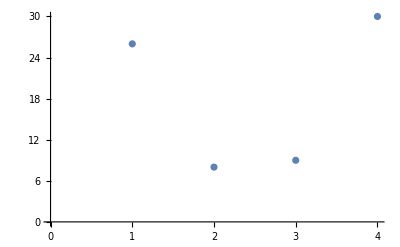

```mathematica
ListPlot[patientsPerMonth[[All,1]][[All,2]]]
```

```mathematica
patientsPerMonth[[All,1]][[All,2]]
```

{26,8,9,30}

```mathematica
ListPlot[{26,8,9,30}]
```

-Graphics-

```mathematica
Table[
BarChart[
Labeled[#,#]&/@Table[patientsPerMonth[[All,index]][[All,2]][[n]],{n,4}],
PlotLabel->patientsPerMonth[[All,index]][[All,1]][[1]],ChartStyle->"DarkRainbow",ChartLegends->{"2011","2012","2013","2014"},FrameLabel->{"Same-Month Frequency
of Suspected Malaria Cases
in the Study Area"},Frame->True]
,{index,1,12}]
```

-Graphics-

```mathematica
patientsPerMonth[[All,2]]
```

{{February,26},{February,65},{February,12},{February,36}}